# Velocity and Acceleration Graph

```mathematica
Velocity and acceleration graphs provide essential insights into the motion of objects over time,crucial in physics,engineering,and other disciplines.In a velocity graph,the velocity of an object is plotted on the y-axis against time on the x-axis.The slope of the velocity graph represents the object's acceleration:a positive slope indicates acceleration in the positive direction,a negative slope indicates acceleration in the negative direction,and a horizontal line represents constant velocity (zero acceleration).Changes in slope signify changes in acceleration,such as speeding up,slowing down,or changing direction.Conversely,an acceleration graph depicts acceleration against time,with time on the x-axis and acceleration on the y-axis.The area under the acceleration graph corresponds to changes in velocity:positive area represents an increase in velocity (speeding up),negative area represents a decrease in velocity (slowing down),and zero area indicates constant velocity.Moreover,the slope of the acceleration graph represents the rate of change of acceleration,providing insights into how quickly the object's acceleration is changing.Together,these graphs offer a comprehensive visualization of an object's motion,facilitating the analysis of its velocity changes,accelerations,and overall dynamics.By interpreting velocity and acceleration graphs,scientists,engineers,and analysts can gain deeper insights into the behavior of moving objects and make informed decisions in various applications,such as designing transportation systems,optimizing machinery performance,and predicting the trajectories of celestial bodies.
```

```mathematica
"An object is moving along a straight line with a acceleration a(t)=12t-6 m/s^2. If v(1)=9 m/s and s(1)= 15 m,find v(t) and s(t)."
DSolve[{v'[t]==12t-6, v[1]==9},v[t],t]
```

An object is moving along a straight line with a acceleration a(t)=12t-6 m/s^2. If v(1)=9 m/s and s(1)= 15 m,find v(t) and s(t).

{{v[t]→3 (3-2 t+2 t^2)}}

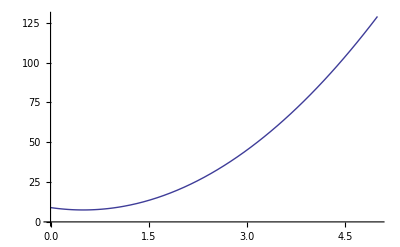

```mathematica
Plot[{3 (3-2 t+2 t^2)},{t,0,5}]
```

```mathematica
DSolve[{s''[t]==12t-6,s[1]==15 ,s'[1]==9},s[t],t]
```

{{s[t]→7+9 t-3 t^2+2 t^3}}

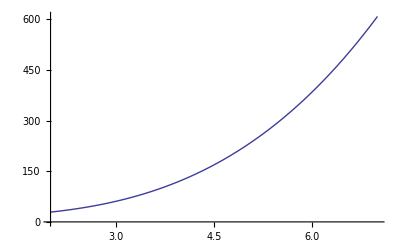

```mathematica
Plot[{7+9 t-3 t^2+2 t^3},{t,2,7}]
```

```mathematica
"An object is moving along a straight line with a acceleration a(t)=2t-8 m/s^2. If v(0)=0 m/s and s(0)= 10 m,find v(t) and s(t)."
```

```mathematica
DSolve[{v'[t]==2t-8,v[0]==0},v[t],t]
```

{{v[t]→-8 t+t^2}}

```mathematica
DSolve[{s''[t]==2t-8,s[0]==10,s'[0]==0},s[t],t]
```

{{s[t]→1/3 (30-12 t^2+t^3)}}

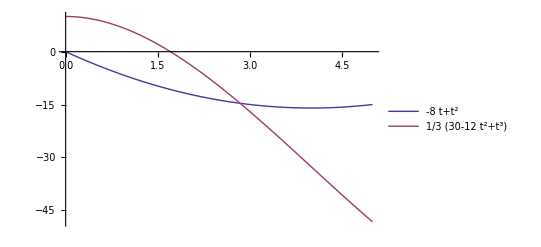

```mathematica
Plot[{-8 t+t^2,1/3 (30-12 t^2+t^3)},{t,0,5},PlotLegends->"Expressions"]
```